# Kerr Geodesics

The KerrGeodesics package provides functions for computing quantities related to bound timelike geodesic orbits in Kerr spacetime. The package is part of the Black Hole Perturbation Toolkit (bhptoolkit.org). Before using the functions, first load the package:

```mathematica
<<KerrGeodesics`
```

For a given black hole spin a geodesic can be unique parametrized (up to orientation) by the orbital Energy, ℰ, angular momentum, ℒ, and Carter constant, 𝒬. An alternative parameterization is given by the semi-latus rectum, p, orbital eccentricity, e, and an inclination angle. There are a few inclination angles used in the literature. In the Toolkit we opt to use x_inc=Cos[θ_inc]. The angle θ_inc relates to the minimum angle obtained during the orbital motion, θ_min by θ_inc = π/2 - Sign[ℒ]θ_min. Equatorial prograde orbits have x_inc=1, equatorial retrograde orbits have x_inc=-1 and polar orbits have x_inc=0.

For all orbits we take 0≤ a≤1 and use the inclination angle to differentiate between prograde and retrograde orbits.

### Constants of motion

The constants of motion can be found individually

```mathematica
KerrGeoEnergy[0.9,10,0.5,Cos[π/4]]
KerrGeoAngularMomentum[0.9,10,0.5,Cos[π/4]]
KerrGeoCarterConstant[0.9,10,0.5,Cos[π/4]]
```

0.964292

2.52602

6.40919

They can also be computed together, and at arbitrary precision

```mathematica
KerrGeoConstantsOfMotion[0.9`20,10,0.5`20,Cos[π/4]]
```

{0.964292350042620738,2.5260208894763507,6.409188340848852}

Some cases can be evaluated analytically, e.g., Schwarzschild orbits

```mathematica
KerrGeoConstantsOfMotion[0,p,e,1]
```

{√((-4 e^2+(-2+p)^2)/(p (-3-e^2+p))),p/(√(-3-e^2+p)),0}

Or polar, eccentric orbits in Kerr spacetime

```mathematica
KerrGeoConstantsOfMotion[a,p,e,0]
```

{√(-(p (a^4 (-1+e^2)^2+(-4 e^2+(-2+p)^2) p^2+2 a^2 p (-2+p+e^2 (2+p))))/(a^4 (-1+e^2)^2 (-1+e^2-p)+(3+e^2-p) p^4-2 a^2 p^2 (-1-e^4+p+e^2 (2+p)))),0,-(p^2 (a^4 (-1+e^2)^2+p^4+2 a^2 p (-2+p+e^2 (2+p))))/(a^4 (-1+e^2)^2 (-1+e^2-p)+(3+e^2-p) p^4-2 a^2 p^2 (-1-e^4+p+e^2 (2+p)))}

### Orbital frequencies

By default the orbital frequencies are computed with respect to the time of the asymptotic observer (t-time in Boyer-Lindquist coordinates)

```mathematica
KerrGeoFrequencies[0.9,5,0.7,Cos[π/3]]
```

{0.0189922,0.0472676,0.0568133}

You can also computed them w.r.t. Mino time

```mathematica
KerrGeoFrequencies[0.9`20,5,0.7`20,Cos[π/3],Time->"Mino"]
```

{1.2436580351157,3.09519881035764,3.7202771085}

Some cases can be evaluated analytically

```mathematica
KerrGeoFrequencies[0,p,e,x,Time->"Mino"]
```

{(√(-(p (-6+2 e+p))/(3+e^2-p)) π)/(2 EllipticK[(4 e)/(-6+2 e+p)]),p √(1/((-3-e^2+p) x^2)) x,(p x)/(√((-3-e^2+p) x^2))}

### Special orbits: ISCO, separatrix, photon sphere, IBSO and ISSO

#### ISCO

Radius of the ISCO for prograde and retrograde orbits for given a

```mathematica
KerrGeoISCO[0.99`20,1]
KerrGeoISCO[0.99`20,-1]
KerrGeoISCO[a,1]
```

1.45449793805967163

8.971861342546968144

3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)))

#### Separatrix

Simple cases are known analytically

```mathematica
KerrGeoSeparatrix[0,e,1]
KerrGeoSeparatrix[1,e,1]
```

6+2 e

1+e

Find the value of p_s at the separatrix for generic orbits given (a,e,x_inc)

```mathematica
KerrGeoSeparatrix[0.9`20,0.5`20,Cos[π/3]]
```

4.34225968111275

Plot the separatrix for various inclinations for a rapidly rotating black hole

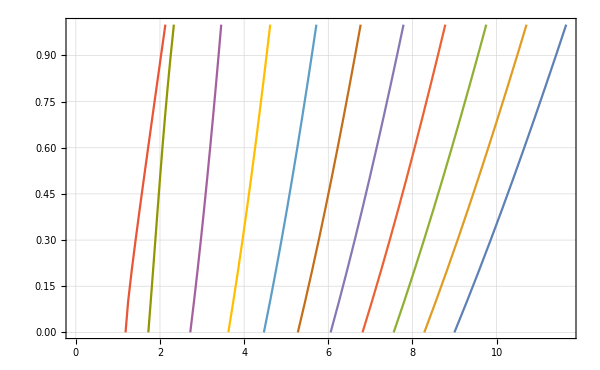

```mathematica
res=Table[{KerrGeoSeparatrix[0.999,e,x],e},{x,-1,1,0.2},{e,0,1,0.1}]//Quiet;
ListPlot[res,Joined->True,PlotTheme->"Detailed",ImageSize->600]
```

#### Photon sphere

The photon sphere radius is known analytically for a few special cases

```mathematica
KerrGeoPhotonSphereRadius[a,1]
KerrGeoPhotonSphereRadius[1,x]
KerrGeoPhotonSphereRadius[a,0]
```

2 (1+Cos[(2 ArcCos[-a])/3])

If[x<-1+√3,1+√2 √(1-x)-x,1]

1+2 √(1-a^2/3) Cos[1/3 ArcCos[(1-a^2)/((1-a^2/3)^(3/2))]]

Evaluate it numerically to arbitrary precision

```mathematica
KerrGeoPhotonSphereRadius[0.998`20,Cos[3π/4]]
```

3.554198335849762503

Plot the photon sphere radius for a number of different black hole spins

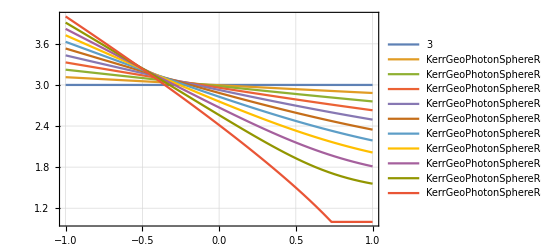

```mathematica
Plot[Table[KerrGeoPhotonSphereRadius[a,x],{a,0,1,0.1}]//Evaluate,{x,-1,1},PlotTheme->"Detailed"]
```

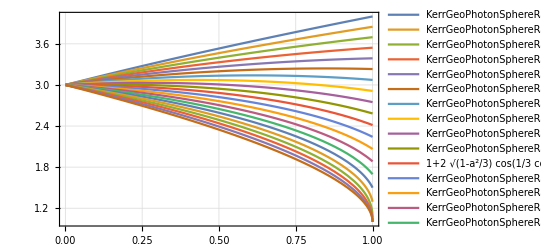

```mathematica
Plot[Table[KerrGeoPhotonSphereRadius[a,x],{x,-1,1,0.1}]//Evaluate,{a,0.001,1},PlotTheme->"Detailed"]
```

#### IBSO

You can also calculate the radius of the inner-most bound spherical orbit

```mathematica
KerrGeoIBSO[a,1]
KerrGeoIBSO[1,0]
KerrGeoIBSO[0.9`40,Cos[π/9]]
```

2+2 √(1-a)-a

1+1/(√(6/(4+4/(19+3 √33)^(1/3)+(19+3 √33)^(1/3))))+1/(√(6/(8-4/(19+3 √33)^(1/3)-(19+3 √33)^(1/3)+6 √(6/(4+4/(19+3 √33)^(1/3)+(19+3 √33)^(1/3))))))

1.78898318826174570217569585438744539593

#### ISSO

You can also calculate the radius of the inner-most stable spherical orbit. For equatorial orbits r_ISSO=r_ISCO

```mathematica
KerrGeoISSO[a,1]==KerrGeoISCO[a,1]
```

True

```mathematica
KerrGeoISSO[1,0]
```

1+√3+√(3+2 √3)

```mathematica
KerrGeoISSO[0.8`40,0.6`40]
```

3.8630278508110029658311749903574469

### Compute the orbital trajectory

The function KerrGeoOrbit computes the orbital trajectory and various properties of the orbit. The function returns a KerrGeoOrbitFunction which can be queried for various information about the orbit. In general there are two methods to compute the trajectory numerically (following arXiv:1506.04742) and analytically (following arXiv:0906.1420).

```mathematica
orbit=KerrGeoOrbit[0.98,5,0.7,Cos[π/4]]
```

KerrGeoOrbitFunction[0.98,5,0.7,0.707107,<<>>]

The KerrGeoOrbitFunction[] can be queried for various properties of the orbit

```mathematica
{orbit["Energy"],orbit["AngularMomentum"],orbit["CarterConstant"]}
orbit["ConstantsOfMotion"]
orbit["Frequencies"]
orbit["RadialRoots"]
```

{0.952482,2.00489,4.06414}

{0.952482,2.00489,4.06414}

{1.68389,2.8471,3.37348}

{16.6667,2.94118,1.27641,0.672375}

You can also extract functions for the orbital trajectory

```mathematica
{t,r,θ,ϕ}=orbit["Trajectory"];
```

Evaluating these functions is equivalent to evaluating the KerrGeoOrbitFunction[]

```mathematica
{t[λ],r[λ],θ[λ],ϕ[λ]}/.λ->10
orbit[10]
```

{810.167,6.17244,2.33715,33.5876}

{810.167,6.17244,2.33715,33.5876}

#### Equatorial orbits

For equatorial orbits you can parametrize the orbit by either Mino time, λ, or the Darwin relativistic anomaly, χ.

```mathematica
orbitMino=KerrGeoOrbit[0.9,7,0.7,1]
orbitDarwin=KerrGeoOrbit[0.9,7,0.7,1,Parametrization->"Darwin"]
```

KerrGeoOrbitFunction[0.9,7,0.7,1.,<<>>]

KerrGeoOrbitFunction[0.9,7,0.7,1.,<<>>]

```mathematica
orbitMino[1]
orbitDarwin[1]
```

{56.2517,12.0801,1.5708,3.40927}

{15.0598,5.07905,1.5708,1.65739}

```mathematica
{tM,rM,θM,ϕM}=orbitMino["Trajectory"];
{tD,rD,θD,ϕD}=orbitDarwin["Trajectory"];
```

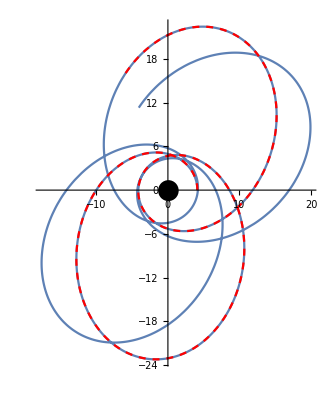

```mathematica
Show[
ParametricPlot[{rM[λ] Cos[ϕM[λ]],rM[λ] Sin[ϕM[λ]]},{λ,0,10}],
ParametricPlot[{rD[χ] Cos[ϕD[χ]],rD[χ] Sin[ϕD[χ]]},{χ,0,10},PlotStyle->{Red,Dashed}],
Graphics[Disk[{0,0},1+Sqrt[1-0.9^2]]]
]
```

#### Generic, non-equatorial orbits

For these orbits you can only use Mino time as a parametrization

```mathematica
orbit=KerrGeoOrbit[0.99,4,0.6,Cos[π/4]];
```

```mathematica
{t,r,θ,ϕ}=orbit["Trajectory"];
```

```mathematica
Show[
ParametricPlot3D[{r[λ]Sin[θ[λ]]Cos[ϕ[λ]],r[λ]Sin[θ[λ]]Sin[ϕ[λ]],r[λ]Cos[θ[λ]]},{λ,0,10},ImageSize->800],
Graphics3D[Sphere[{0,0,0},1+Sqrt[1-0.99^2]]]
]
```

-Graphics3D-

Plot the motion in the {r, Cos[θ]} plane

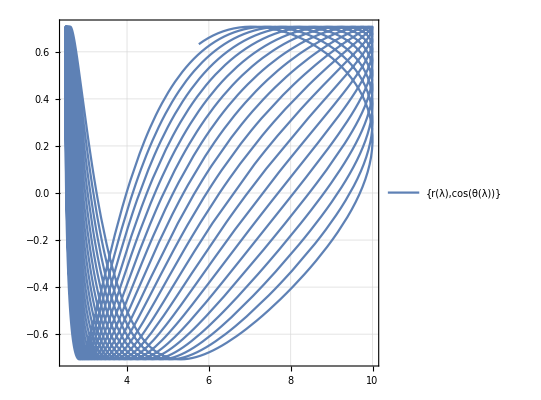

```mathematica
ParametricPlot[{r[λ],Cos[θ[λ]]},{λ,0,50},AspectRatio->1,PlotTheme->"Detailed"]
```

ToDo: Show a resonant orbit and show how it changes as you change the orbital phases

#### Numerical vs analytic evaluation

There are two methods for computing the orbital trajectory. The numerical method takes longer to compute the KerrGeoOrbitFunction but then that function is faster to evaluate. Conversely the analytic method is quick to compute the KerrGeoOrbitFunction but then that function is slower to evaluate/

```mathematica
Timing[orbitN=KerrGeoOrbit[0.99,4,0.6,Cos[π/4]]]
Timing[orbitA=KerrGeoOrbit[0.99,4,0.6,Cos[π/4],Method->"Analytic"]]
```

{0.093833,KerrGeoOrbitFunction[0.99,4,0.6,0.707107,<<>>]}

{0.007928,KerrGeoOrbitFunction[0.99,4,0.6,0.707107,<<>>]}

```mathematica
Timing[orbitN[10]]
Timing[orbitA[10]]
```

{0.000498,{381.846,2.7104,1.41462,33.907}}

{0.002889,{381.846,2.7104,1.41462,33.907}}

The numerical method is best for plotting the orbit

```mathematica
<<KerrGeodesics`
```

```mathematica
Manipulate[
Block[{orbit,t,r,θ,ϕ,stable,rmax},
stable=False;
rmax=p/(1-e);
If[p>Quiet[KerrGeoSeparatrix[a,e,x]],
stable=True;
orbit=KerrGeoOrbit[a,p,e,x];
{t,r,θ,ϕ}=orbit["Trajectory"];
,{t,r,θ,ϕ}={0,0,0,0}];
Show[
ParametricPlot3D[{r[λ]Sin[θ[λ]]Cos[ϕ[λ]],r[λ]Sin[θ[λ]]Sin[ϕ[λ]],r[λ]Cos[θ[λ]]},{λ,0,10},PlotRange->{{-rmax,rmax},{-rmax,rmax},{-rmax,rmax}},ImageSize->800],
Graphics3D[Sphere[{0,0,0},1+Sqrt[1-0.99^2]]]
]

]
,{{a,0.9},0.000001,0.9999},{{p,10.1},1,12},{{e,0.5},0.000001,0.8},{{x,-0.5},-1,1}
]
```